```mathematica
(*This notebook was not created by the author of the thesis "Microscopic Models for the Haagerup Fusion Category". It is copied from the source code of the following paper:
Scott Morrison,Emily Peters,and Noah Snyder.Categories generated by a trivalent vertex.Selecta Math.,23(2):817–868,2017,10.1007/s00029-016-0240-3. arXiv:1501.06869.*)
```

```mathematica
(*----------------*)
```

```mathematica
(* This is a fork of Polyhedra.nb from the "exceptional" project, made for the sake of standalone code for the arXiv version of the "trivalent" project. Please do not make modifications here. *)
```

## Polyhedra

```mathematica
If[$VersionNumber<8,
<<"Combinatorica`";
UndirectedEdge=List;
IsomorphicGraphQ=Combinatorica`IsomorphicQ;
]
```

```mathematica
ToGraph[z_]:=(If[!FreeQ[z,Diagram],Print["bad argument passed to ToGraph: ",z];Abort[]];If[$VersionNumber<8,FromUnorderedPairs,Graph][UndirectedEdge@@#&/@(List@@Position[z,#]⟦All,1⟧&/@Union[Cases[z,_Integer,∞]])])
```

### The polyhedra database

```mathematica
PolyhedraNames={};
```

```mathematica
getDirectory[]:=getDirectory[]=NotebookDirectory[]
```

```mathematica
SavePolyhedraNames[]:=Put[PolyhedraNames,FileNameJoin[{getDirectory[],"polyhedraNames.m"}]];
LoadPolyhedraNames[]:=(PolyhedraNames=Union[PolyhedraNames,Check[Get[FileNameJoin[{getDirectory[],"polyhedraNames.m"}]],{},Get::noopen]];)
```

```mathematica
NamePolyhedron[G_]:=Module[{r=ToGraph[G],name},
name=Unique["p"];
AppendTo[PolyhedraNames,name->G];
Print["Naming a new polyhedron: ",name->showGraph[r], " ",G];
name
]
```

```mathematica
IdentifyPolyhedron[G_]:=Module[{found,name},
found=Cases[PolyhedraNames,(name_->H_/;IsomorphicGraphQ[ToGraph[H],ToGraph[G]]):>name];
If[Length[found]>1,
Print["Warning! PolyhedraNames contains isomorphs."];Abort[],
If[Length[found]==0,
name=NamePolyhedron[G],
found⟦1⟧
]
]
]
```

```mathematica
IdentifyPolyhedron[d^(k_.)z_.]:=d^k IdentifyPolyhedron[z]
IdentifyPolyhedron[b^(k_.)z_.]:=b^k IdentifyPolyhedron[z]
IdentifyPolyhedron[t^(k_.)z_.]:=t^k IdentifyPolyhedron[z]
IdentifyPolyhedron[Q^(k_.)z_.]:=Q^k IdentifyPolyhedron[z]
IdentifyPolyhedron[n_Integer]:=n
```

```mathematica
IdentifyPolyhedra[polyhedron_]:=Module[{constant,arrays,Ys},
Ys=Union[Cases[polyhedron,_X|_Y|_P,∞]];
If[Ys==={},polyhedron,
arrays=CoefficientArrays[polyhedron,Ys];
constant=arrays⟦1⟧;
arrays=Rest[arrays];
Together[constant+Plus@@Cases[Flatten[ArrayRules/@arrays],(i:{__Integer}->c_):>IdentifyPolyhedron[Times@@Ys⟦i⟧]c]]
]
]
```

```mathematica
If[$VersionNumber<8,
showGraph=GraphPlot[#,Method->"SpringEmbedding"]&,
showGraph=#&
];
```

```mathematica
DisplayPolyhedraNames[]:=#⟦1⟧->showGraph[ToGraph[#⟦2⟧]]&/@PolyhedraNames
```

```mathematica
LoadPolyhedraNames[]
```

```mathematica
SavePolyhedraNames[]
```

### Polyhedra identities

```mathematica
SkeinContexts={"SO(3)","Deligne","Vogel","G2","H3",{1,0,1,1,3},{1,0,1,1,4},{1,0,1,1,5},{1,0,1,1,6}};
```

```mathematica
(SkeinContextParentsRules={{A__,n_Integer}:>{{A,n+1}},"SO(3)"->{{1,0,1,1,3}},"Vogel"->{{1,0,1,1,6}},"Deligne"->{{1,0,1,1,5},"Vogel"},"G2"->{{1,0,1,1,4}},"H3"->{{1,0,1,1,4}}})//TableForm
```

{A__,n_Integer}:>{{A,n+1}}
SO(3)→{{1,0,1,1,3}}
Vogel→{{1,0,1,1,6}}
Deligne→{{1,0,1,1,5},Vogel}
G2→{{1,0,1,1,4}}
H3→{{1,0,1,1,4}}

```mathematica
SkeinContextParents[context_]:=Cases[context/.SkeinContextParentsRules,c_/;MemberQ[SkeinContexts,c]]
```

```mathematica
SkeinContextParents[{1,0,1,1,5}]
```

{{1,0,1,1,6}}

```mathematica
VariableSubstitutions[context_]:={}
```

```mathematica
Clear[DiagramReductions]
DiagramReductions[context_]:={}
```

```mathematica
Clear[PolyhedraEvaluationRules]
PolyhedraEvaluationRules[context_]:={}
```

## Evaluating diagrams

### Tiny faces

We always immediately remove loops, monogons, bigons and triangles.

```mathematica
Do[
Y/:RotateLeft[Y[aa_,bb_,cc_],i]RotateLeft[Y[cc_,bb_,dd_],j]:=b P[aa,dd]
,{i,0,2},{j,0,2}]
```

```mathematica
Y[a_,a_,b_]:=0
Y[a_,b_,a_]:=0
Y[b_,a_,a_]:=0
```

```mathematica
SetAttributes[P,Orderless]
```

```mathematica
P[a_,a_]:=d
P/:P[a_,b_]^2:=d
P/:P[a_,b_]P[b_,c_]:=P[a,c]
```

```mathematica
Do[
P/:RotateLeft[Y[a_,b_,c_],i]P[a_,d_]:=Y[b,c,d]
,{i,0,2}]
```

```mathematica
Do[
P/:RotateLeft[X[a_,b_,c_,d_],i]P[a_,e_]:=RotateLeft[Y[e,b,c,d],i]
,{i,0,3}]
```

```mathematica
Do[
Y/:RotateLeft[Y[a_,b_,c_],i]RotateLeft[Y[b_,d_,e_],j]RotateLeft[Y[c_,e_,f_],k]:=t Y[a,d,f]
,{i,0,2},{j,0,2},{k,0,2}]
```

## Diagram properties

```mathematica
Unprotect[ConnectedComponents];
ConnectedComponents[Diagram[_,contents_]]:=Length[timesToList[contents/.X|Y->Yg//.glomRule]]
```

```mathematica
glomRule={Yg[A___,b_,C___]Yg[D___,b_,E___]:>Union[Yg[A,C,D,E,b]]};
```

```mathematica
NumberOfVertices[Diagram[_,contents_]]:=Count[contents,_Y]
```

```mathematica
NumberOfInternalFaces[d:Diagram[boundary_,contents_]]:=NumberOfInternalFaces[d]=1/2 NumberOfVertices[d]+ConnectedComponents[d]-1/2 Length[boundary]
```

```mathematica
Clear[Diagram]
```

```mathematica
Diagram/:Diagram[{A___,b_,C___},c1_]Diagram[{D___,b_,E___},c2_]:=Module[{newContents},
newContents=Collect[c1 c2,_Y|_P,Together];
Diagram[{A,E,D,C},newContents]
]
Diagram[{A___,b_,b_,C___},contents_]:=Diagram[{A,C},contents]
Diagram[{b_,A___,b_},contents_]:=Diagram[{A},contents]
```

```mathematica
(*Diagram/:α_ Diagram[bdy_,contents_]:=Diagram[bdy,α contents]
 Diagram/:Diagram[{A___,C___},c1_]+Diagram[{C___,A___},c2_]:=Diagram[{A,C},c1+c2]*)
```

## Enumerating diagrams

### Canonical labelling and isomorphism

```mathematica
timesToList[X_Times]:=List@@X
timesToList[X_List]:=X
timesToList[X_]:={X}
```

```mathematica
canonicalLabellingCounter=0;
```

```mathematica
K0=10000000;
```

```mathematica
Clear[canonicalLabelling]
canonicalLabelling[d:Diagram[boundary_,contents_]]:=canonicalLabelling[d]=Module[{limit=20,m0=K0,m,labels,newLabels,newBoundary,boundaryReplacements,Yrule,c,t,r,sortOrder},
canonicalLabellingCounter--;
sortOrder[2]=0;
sortOrder[1]=1;
sortOrder[_]=2;
labels=Union[Flatten[Cases[contents,x:(_Y|_P):>List@@x,∞]]];
newLabels=Thread[labels->Range[Length[labels]]];
m:=(m0++);
newBoundary=Table[m,{Length[boundary]}];
boundaryReplacements=Thread[(boundary/.newLabels)->newBoundary];
c=timesToList[contents/.(x:(_Y|_P):>(x/.newLabels/.boundaryReplacements))];
Yrule=y_Y:>Sort[{y,RotateLeft[y],RotateRight[y]}]⟦1⟧;
c=c/.Yrule;
While[c=!=0∧limit-->0∧!FreeQ[Cases[c,x:(_Y|_P):>List@@x,∞],n_Integer/;n<K0]∧Count[c,_Y]>0,
t=SortBy[Cases[c,_Y,∞],With[{ns=Sort[Cases[(List@@#),n_/;n≥K0]]},{sortOrder[Length[ns]],ns}]&]⟦1⟧;
r=If[Count[List@@t,n_/;n<K0]==1,
Cases[List@@t,n_/;n<K0]⟦1⟧->m,
t⟦Mod[Position[List@@t,n_/;n≥K0]⟦1,1⟧,3]+1⟧->m
];
c=c/.(z:(_Y|_P):>(z/.r));
c=c/.Yrule;
];
If[limit<0,Print["canonicalLabelling took too long! ",d];Abort[]];
Diagram[newBoundary,If[Head[contents]===List,Sort[c],Times@@c]]
]
canonicalLabelling[d:Diagram[{},_]]:=d
```

```mathematica
canonicalLabelling[x_ d_Diagram]:=x canonicalLabelling[d]
```

```mathematica
canonicalLabelling[0]:=0
```

```mathematica
DiagramsIsomorphicQ[d1_Diagram,d2_Diagram]:=canonicalLabelling[d1]===canonicalLabelling[d2]
```

### Generating diagrams

It would be nice to replace this with something based on plantri!

```mathematica
k0=10000;
freshLabel:=k0++
```

```mathematica
Clear[diagramsByVertexNumber]
```

```mathematica
diagramsByVertexNumber[0,0]:={Diagram[{},{}]}
diagramsByVertexNumber[1,1]:={}
diagramsByVertexNumber[n_Integer/;n<0,_]:={}
diagramsByVertexNumber[_Integer,k_Integer/;k<0]:={}
```

```mathematica
diagramsByVertexNumber[n_Integer,k_Integer]:=diagramsByVertexNumber[n,k]=isomorphismRepresentatives[isomorphismRepresentatives[addCups[diagramsByVertexNumber[n-2,k]]]~Join~isomorphismRepresentatives[addForks[diagramsByVertexNumber[n-1,k-1]]]~Join~isomorphismRepresentatives[addHs[diagramsByVertexNumber[n,k-2]]]]
```

```mathematica
addCups[X_List]:=Flatten[addCups/@X]
addForks[X_List]:=Flatten[addForks/@X]
addHs[X_List]:=Flatten[addHs/@X]
```

```mathematica
addCups[Diagram[boundary_,contents_]]:=With[{k1=freshLabel,k2=freshLabel},Table[Diagram[RotateRight[RotateLeft[boundary,i]~Join~{k1,k2},i],Append[contents, P[k1,k2]]],{i,0,Length[boundary]}]]
```

```mathematica
addY[contents_,x_,y_,z_]:=Module[{x0,Ps},
Ps=Cases[contents,P[x,_],1,1];
If[Length[Ps]>0,
x0=DeleteCases[(List@@Ps⟦1⟧),x]⟦1⟧;
Append[DeleteCases[contents,P[x,x0]],Y[x0,y,z]],
Append[contents,Y[x,y,z]]
]
]
```

```mathematica
addForks[Diagram[boundary_,contents_]]:=
With[{k1=freshLabel,k2=freshLabel},
Table[Diagram[Take[boundary,i]~Join~{k1,k2}~Join~Drop[boundary,i+1],addY[contents,boundary⟦i+1⟧,k1,k2]],{i,0,Length[boundary]-1}]~Join~{Diagram[{k2}~Join~Most[boundary]~Join~{k1},addY[contents,boundary⟦-1⟧,k1,k2]],Diagram[{k1,k2}~Join~Most[boundary],addY[contents,boundary⟦-1⟧,k1,k2]]}
]
```

```mathematica
addHs[dd:Diagram[boundary_,contents_]]:=
Module[{k1=freshLabel,k2=freshLabel,k3=freshLabel,aa,bb},
DeleteCases[Table[
{aa,bb}={boundary⟦i+1⟧,boundary⟦Mod[i+1,Length[boundary]]+1⟧};
(* If we're attached to a fork, don't bother. If we're attached to an arc, addForks will do it instead. *)
If[MemberQ[contents,P[aa,_]|P[_,bb]|Y[aa,bb,_]|Y[_,aa,bb]|Y[bb,_,aa]],
0,
Diagram[RotateRight[{k1,k2}~Join~Drop[RotateLeft[boundary,i],2],i],contents~Join~{Y[aa,k1,k3],Y[bb,k3,k2]}]
],
{i,0,Length[boundary]-1}
],0
]
]
```

```mathematica
isomorphismRepresentatives[X_List]:=Module[{representatives={}},
canonicalLabellingCounter=Length[X];
Do[With[{c=canonicalLabelling[x]},
If[!MemberQ[representatives,c],AppendTo[representatives,c]]
],{x,X}];
representatives
]
```

```mathematica
Clear[Diagrams]
Diagrams[n_Integer,k_Integer]:=Diagrams[n,k]=Cases[Join@@Table[Diagram[#⟦1⟧,Times@@#⟦2⟧]&/@diagramsByVertexNumber[n,m],{m,Mod[n,2],n+2k-2,2}],d_/;NumberOfInternalFaces[d]==k]
Diagrams[n_Integer,_≤k_Integer]:=Join@@Table[Diagrams[n,i],{i,0,k}]
```

```mathematica
SaveDiagrams[]:=Module[{},
If[FileExistsQ[FileNameJoin[{getDirectory[],"diagramsByVertexNumber.m"}]],DownValues[diagramsByVertexNumber]=Union[Get[FileNameJoin[{getDirectory[],"diagramsByVertexNumber.m"}]]~Join~DownValues[diagramsByVertexNumber],SameTest->(#1⟦1⟧==#2⟦1⟧&)]];
Put[DownValues[diagramsByVertexNumber],FileNameJoin[{getDirectory[],"diagramsByVertexNumber.m"}]];
]
```

### Locating faces

```mathematica
PartialFace/:PartialFace[A___,b_,c_]PartialFace[b_,c_,D___]:=PartialFace[A,b,c,D]
```

```mathematica
PartialFace[A___,{b_,i_},C___]:=PartialFace[A,b,C]
```

```mathematica
PartialFace[a_,b_,C___,a_,b_]:=Face[a,b,C]
```

```mathematica
Faces[diagram_]:=List@@((diagram/.P[a_,b_]:>PartialFace[a,b]PartialFace[b,a]//.Flatten[Table[RotateLeft[Y[a_,b_,c_],i]RotateLeft[Y[c_,d_,e_],j]:>PartialFace[a,c,e]PartialFace[d,c,b]Y[a,b,{c,1}]Y[{c,2},d,e],{i,0,2},{j,0,2}]])/._Y:>1)
```

```mathematica
Faces[Diagram[boundary_,content_]]:=Faces[content]
```

```mathematica
edgesIncidentToCycle[Ys_,cycle_]:=Table[With[{a=cycle⟦i⟧,b=cycle⟦Mod[i,Length[cycle]]+1⟧},(Cases[Ys,Y[a,b,c_]|Y[c_,a,b]|Y[b,c_,a]:>{c,1}]~Join~Cases[Ys,Y[b,a,c_]|Y[c_,b,a]|Y[a,c_,b]:>{c,-1}])⟦1⟧],{i,1,Length[cycle]}]
```

```mathematica
edgesLeftOfCycle[Ys_,cycle_]:=Cases[edgesIncidentToCycle[Ys,cycle],{x_,-1}:>x]
```

```mathematica
FindSquares[dd_Diagram]:=Cases[Faces[dd],Face[a_,b_,c_,d_]:>Module[{Ys},
Ys=Cases[dd⟦2⟧,y_Y/;Count[y,a|b|c|d]==2];
Diagram[edgesLeftOfCycle[Ys,{a,b,c,d}],Times@@Ys]
]]
```

```mathematica
FindPentagons[dd_Diagram]:=Cases[Faces[dd],Face[a_,b_,c_,d_,e_]:>Module[{Ys},
Ys=Cases[dd⟦2⟧,y_Y/;Count[y,a|b|c|d|e]==2];
Diagram[edgesLeftOfCycle[Ys,{a,b,c,d,e}],Times@@Ys]
]]
```

```mathematica
FindAdjacentPolygons[n1_,n2_][dd_Diagram]:=FindAdjacentPolygons[n1,n2][dd]=
Module[{faces=Faces[dd],pairs,unpackPair,bdy},
pairs=Flatten[Table[{f1,f2},{f1,Cases[faces,f_Face/;Length[f]==n1]},{f2,Cases[faces,f_Face/;Length[f]==n2∧Length[Intersection[f,f1]]==1]}],1];
unpackPair[{Face[A___,b_,C___],Face[D___,b_,E___]}]:=Module[{Ys},
Ys=Cases[dd⟦2⟧,y_Y/;Count[y,A|C|D|E]==2];
If[Length[Ys]≠n1+n2-2,Print["FindAdjacentPolygons failed..."];Abort[]];
bdy=edgesLeftOfCycle[Ys,{A,E,D,C}];
(* where does the boundary go? the first edge coming out of the n2 polygon *)
If[Length[{A}]≥2,bdy=RotateLeft[bdy,Length[{A}]-1]];
If[Length[bdy]≠n1+n2-4,Print["FindAdjacentPolygons failed..."];Abort[]];
Diagram[bdy,Times@@Ys]
];
unpackPair/@pairs
]
```

```mathematica
FindAdjacentSquares=FindAdjacentPolygons[4,4];
FindPentasquares=FindAdjacentPolygons[4,5];
```

```mathematica
Clear[DiagramsWithoutSquares,DiagramsWithoutAdjacentSquares,DiagramsWithoutSmallPairs]
DiagramsWithoutSquares[n_Integer,k_Integer]:=DiagramsWithoutSquares[n,k]=Cases[Diagrams[n,k],d_/;Length[FindSquares[d]]==0]
DiagramsWithoutAdjacentSquares[n_Integer,k_Integer]:=DiagramsWithoutAdjacentSquares[n,k]=Cases[Diagrams[n,k],d_/;Length[FindAdjacentSquares[d]]==0]
DiagramsWithoutSmallPairs[n_Integer,k_Integer]:=DiagramsWithoutSmallPairs[n,k]=Cases[DiagramsWithoutAdjacentSquares[n,k],d_/;Length[FindPentasquares[d]]==0]
DiagramsWithoutSquares[n_Integer,_≤k_Integer]:=Join@@Table[DiagramsWithoutSquares[n,i],{i,0,k}]
DiagramsWithoutAdjacentSquares[n_Integer,_≤k_Integer]:=Join@@Table[DiagramsWithoutAdjacentSquares[n,i],{i,0,k}]
DiagramsWithoutSmallPairs[n_Integer,_≤k_Integer]:=Join@@Table[DiagramsWithoutSmallPairs[n,i],{i,0,k}]
```

```mathematica
Do[
Yb/:RotateLeft[Yb[a_,e_,h_],i]RotateLeft[Yb[b_,f_,e_],j]RotateLeft[Yb[c_,g_,f_],k]RotateLeft[Yb[d_,h_,g_],l]:=P[a,c]P[b,d]
,{i,0,2},{j,0,2},{k,0,2},{l,0,2}]
```

```mathematica
BraidedComponents[Diagram[_,contents_]]:=Length[timesToList[contents/.Y->Yb/.Yb->Y/.Y->Yg//.glomRule]]
```

```mathematica
ConnectedDiagrams[n_Integer,k_]:=Cases[Diagrams[n,k],d_/;BraidedComponents[d]==1]
```

```mathematica
ConnectedDiagramsWithoutSquares[n_Integer,k_]:=Cases[DiagramsWithoutSquares[n,k],d_/;BraidedComponents[d]==1]
```

```mathematica
ConnectedDiagramsWithoutSmallPairs[n_Integer,k_]:=Cases[DiagramsWithoutSmallPairs[n,k],d_/;BraidedComponents[d]==1]
```

## Inner products

```mathematica
Clear[InnerProduct]
InnerProduct[d1_Diagram,d2_Diagram]:=InnerProduct[d1,d2]=Module[{k=Length[d1⟦1⟧],max1=Max[Cases[d1,_Integer,∞]],min2=Min[Cases[d2,_Integer,∞]],δ},
δ=max1-min2+1;
IdentifyPolyhedra[Product[P[d1⟦1,i⟧,d2⟦1,k+1-i⟧+δ],{i,1,k}]d1⟦2⟧(d2⟦2⟧/.(c:(_Y|_P):>(c/.n_Integer:>n+δ)))]
]
```

```mathematica
InnerProducts[n_,k_]:=Outer[InnerProduct,Diagrams[n,_≤k],Diagrams[n,_≤k]]
```

```mathematica
InnerProductsWithoutSquares[n_,k_]:=Outer[InnerProduct,DiagramsWithoutSquares[n,_≤k],DiagramsWithoutSquares[n,_≤k]]
```

```mathematica
InnerProductsWithoutAdjacentSquares[n_,k_]:=Outer[InnerProduct,DiagramsWithoutAdjacentSquares[n,_≤k],DiagramsWithoutAdjacentSquares[n,_≤k]]
```

```mathematica
InnerProductsWithoutSmallPairs[n_,k_]:=Outer[InnerProduct,DiagramsWithoutSmallPairs[n,_≤k],DiagramsWithoutSmallPairs[n,_≤k]]
```

## Applying relations

```mathematica
AddPolyhedraEvaluations[context_][X_]:=Module[{},
PolyhedraEvaluationRules[context]=Union[PolyhedraEvaluationRules[context],Cases[X,(name_->value_)/;MemberQ[PolyhedraNames⟦All,1⟧,name],∞]];
PolyhedraEvaluationRules[context]=PolyhedraEvaluationRules[context]/.(name_->value_):>(name->Together[(value//.PolyhedraEvaluationRules[context]/.VariableSubstitutions[context])]);
]
```

```mathematica
Clear[AddDiagramReduction]
AddDiagramReduction[context_][X_]:=(DiagramReductions[context]=Union[DiagramReductions[context],{X}];)
```

```mathematica
labels[stuff_]:=Union[Flatten[Cases[stuff,Y[a_,b_,c_]:>{a,b,c},{0,∞}]~Join~Cases[stuff,P[a_,b_]:>{a,b},{0,∞}]]]
```

```mathematica
refreshInternalLabels[Diagram[b_,c_]]:=Module[{labels=labels[c],internalLabels,replacements},
internalLabels=Complement[labels,b];
replacements=#->freshLabel&/@internalLabels;
Diagram[b,c/.replacements]
]
```

```mathematica
ApplySquareRelation[relation_][D:Diagram[bdy_,contents_]]:=Table[
Module[{newBoundary=square⟦1⟧,replacement,diff},
replacement=Thread[Diagrams[4,0]⟦1,1⟧->newBoundary];
diff=Complement[timesToList[contents],timesToList[square⟦2⟧]];
If[Length[diff]≠Length[timesToList[contents]]-Length[timesToList[square⟦2⟧]],Print["uh oh"];Abort[]];
Sum[relation⟦k⟧Diagram[bdy,(Times@@diff)(refreshInternalLabels[Diagrams[4,0]⟦k⟧]⟦2⟧/.replacement)],{k,1,4}]],
{square,FindSquares[D]}
]
```

```mathematica
ApplyPentagonRelation[relation_][D:Diagram[bdy_,contents_]]:=Table[
Module[{newBoundary=pentagon⟦1⟧,replacement,diff},
replacement=Thread[Diagrams[5,0]⟦1,1⟧->newBoundary];
diff=Complement[timesToList[contents],timesToList[pentagon⟦2⟧]];
If[Length[diff]≠Length[timesToList[contents]]-Length[timesToList[pentagon⟦2⟧]],Print["uh oh"];Abort[]];
Sum[relation⟦k⟧Diagram[bdy,(Times@@diff)(refreshInternalLabels[Diagrams[5,0]⟦k⟧]⟦2⟧/.replacement)],{k,1,10}]],
{pentagon,FindPentagons[D]}
]
```

```mathematica
ApplyAdjacentSquaresRelation[relation_][D:Diagram[bdy_,contents_]]:=Table[
Module[{newBoundary=square⟦1⟧,replacement,diff},
replacement=Thread[Diagrams[4,_≤1]⟦1,1⟧->newBoundary];
diff=Complement[timesToList[contents],timesToList[square⟦2⟧]];
If[Length[diff]≠Length[timesToList[contents]]-Length[timesToList[square⟦2⟧]],Print["uh oh"];Print[diff];Print[timesToList[contents]];Print[timesToList[square⟦2⟧]];Abort[]];
Sum[relation⟦k⟧Diagram[bdy,(Times@@diff)(refreshInternalLabels[Diagrams[4,_≤1]⟦k⟧]⟦2⟧/.replacement)],{k,1,5}]
],
{square,FindAdjacentSquares[D]}
]
```

```mathematica
ApplyPentasquareRelation[relation_][D:Diagram[bdy_,contents_]]:=Table[
Module[{newBoundary=pentasquare⟦1⟧,replacement,diff,diagrams=Diagrams[5,_≤1]},
replacement=Thread[diagrams⟦1,1⟧->newBoundary];
diff=Complement[timesToList[contents],timesToList[pentasquare⟦2⟧]];
If[Length[diff]≠Length[timesToList[contents]]-Length[timesToList[pentasquare⟦2⟧]],Print["uh oh"];Print[diff];Print[timesToList[contents]];Print[timesToList[pentasquare⟦2⟧]];Abort[]];
Sum[relation⟦k⟧Diagram[bdy,(Times@@diff)(refreshInternalLabels[diagrams⟦k⟧]⟦2⟧/.replacement)],{k,1,16}]
],
{pentasquare,FindPentasquares[D]}
]
```

```mathematica
ApplyPentapentRelation[relation_][D:Diagram[bdy_,contents_]]:=Table[
Module[{newBoundary=pentapent⟦1⟧,replacement,diff,diagrams=DiagramsWithoutSquares[6,_≤1]},
replacement=Thread[diagrams⟦1,1⟧->newBoundary];
diff=Complement[timesToList[contents],timesToList[pentapent⟦2⟧]];
If[Length[diff]≠Length[timesToList[contents]]-Length[timesToList[pentapent⟦2⟧]],Print["uh oh"];Print[diff];Print[timesToList[contents]];Print[timesToList[pentapent⟦2⟧]];Abort[]];
Sum[relation⟦k⟧Diagram[bdy,(Times@@diff)(refreshInternalLabels[diagrams⟦k⟧]⟦2⟧/.replacement)],{k,1,41}]
],
{pentapent,FindAdjacentPolygons[5,5][D]}
]
```

```mathematica
ApplyHexapentRelation[relation_][D:Diagram[bdy_,contents_]]:=Table[
Module[{newBoundary=hexapent⟦1⟧,replacement,diff,diagrams=DiagramsWithoutSquares[7,_≤1]},
replacement=Thread[diagrams⟦1,1⟧->newBoundary];
diff=Complement[timesToList[contents],timesToList[hexapent⟦2⟧]];
If[Length[diff]≠Length[timesToList[contents]]-Length[timesToList[hexapent⟦2⟧]],Print["uh oh"];Print[diff];Print[timesToList[contents]];Print[timesToList[hexapent⟦2⟧]];Abort[]];
Sum[relation⟦k⟧Diagram[bdy,(Times@@diff)(refreshInternalLabels[diagrams⟦k⟧]⟦2⟧/.replacement)],{k,1,Length[diagrams]}]
],
{hexapent,FindAdjacentPolygons[6,5][D]}
]
```

```mathematica
ApplySquareRelation[relation_][X_Times]:=ApplySquareRelation[relation][Diagram[{},X]]/.Diagram[{},Y_]:>IdentifyPolyhedra[Y]
```

```mathematica
ApplyAdjacentSquaresRelation[relation_][X_Times]:=ApplyAdjacentSquaresRelation[relation][Diagram[{},X]]/.Diagram[{},Y_]:>IdentifyPolyhedra[Y]
```

```mathematica
ApplyPentasquareRelation[relation_][X_Times]:=ApplyPentasquareRelation[relation][Diagram[{},X]]/.Diagram[{},Y_]:>IdentifyPolyhedra[Y]
```

```mathematica
ApplyPentapentRelation[relation_][X_Times]:=ApplyPentapentRelation[relation][Diagram[{},X]]/.Diagram[{},Y_]:>IdentifyPolyhedra[Y]
```

```mathematica
ApplyHexapentRelation[relation_][X_Times]:=ApplyHexapentRelation[relation][Diagram[{},X]]/.Diagram[{},Y_]:>IdentifyPolyhedra[Y]
```

```mathematica
ApplyDiagramReductions[context_][X_]:=Flatten[Table[Together[dr[X]/.PolyhedraEvaluationRules[context]/.VariableSubstitutions[context]],{dr,DiagramReductions[context]}]]
```

```mathematica
ApplyDiagramReduction[context_][X_]:=Module[{reductions},
reductions=ApplyDiagramReductions[context][X];
If[Length[reductions]>0,reductions⟦1⟧,X]
]
```

```mathematica
FindNewPolyhedronEvaluationRule[context_][P_]:=Module[{results,diffs},
If[MemberQ[First/@PolyhedraEvaluationRules[context],P],
Print["There's already an evaluation rule for ",P],
results=DeleteCases[Union[Factor[ApplyDiagramReductions[context][P/.PolyhedraNames]/.PolyhedraEvaluationRules[context]/.VariableSubstitutions[context]]],P|(P/.PolyhedraNames)];
If[Length[results]==0,
$Failed,
diffs=Union[Together[Rest[results]-First[results]]];
If[diffs==={0}||diffs==={},
AddPolyhedraEvaluations[context][{P->results⟦1⟧}];results⟦1⟧,
Print["Divergent evaluations!"];
Print[results];
$Failed
]
]
]
]
```

```mathematica
ComputeAllPolyhedra[context_]:=Module[{f,names},
names:=SortBy[DeleteCases[PolyhedraNames,(n_->v_)/;MemberQ[PolyhedraEvaluationRules[context],n->_]],Count[#⟦2⟧,_Y,∞]&]⟦All,1⟧;
f=(Print[#->ToGraph[#/.PolyhedraNames]];With[{r=FindNewPolyhedronEvaluationRule[context][#]},Print[r];r])&;
FixedPoint[f/@names&,1];
PolyhedraEvaluationRules[context]=PolyhedraEvaluationRules[context]//.(a_->b_)/;!FreeQ[b,Alternatives@@PolyhedraNames⟦All,1⟧]:>(a->Together[b//.PolyhedraEvaluationRules[context]]);
]
```

```mathematica
SavePolyhedraEvaluations[]:=Module[{},
If[FileExistsQ[FileNameJoin[{getDirectory[],"polyhedraEvaluations.m"}]],
DeleteFile[FileNameJoin[{getDirectory[],"polyhedraEvaluations.m"}]]];
Save[FileNameJoin[{getDirectory[],"polyhedraEvaluations.m"}],PolyhedraEvaluationRules];
]
```

```mathematica
LoadPolyhedraEvaluations[]:=Module[{},
If[FileExistsQ[FileNameJoin[{getDirectory[],"polyhedraEvaluations.m"}]],
Get[FileNameJoin[{getDirectory[],"polyhedraEvaluations.m"}]]];
]
```

## Parallel row reduction

```mathematica
matrixDirectory=FileNameJoin[{getDirectory[],"..","matrices"}];
```

```mathematica
rowFile[token_,i_]:=FileNameJoin[{matrixDirectory,token<>"_"<>StringTake["000"<>ToString[i],-3]}]
```

```mathematica
writeMatrix[token_,M_]:=(Table[Put[M⟦i⟧,rowFile[token,i]],{i,1,Length[M]}];)
readMatrix[token_]:=Table[Get[rowFile[token,i]],{i,1,Length[Get[rowFile[token,1]]]}]
```

```mathematica
If[!FileExistsQ[matrixDirectory],
CreateDirectory[matrixDirectory]
]
```

```mathematica
SetParallel[n_Integer:1]:=Module[{},
CloseKernels[];
LaunchKernels[n];
DistributeDefinitions[rowFile,matrixDirectory,d,b,t];
ParallelEvaluate[t=Global`t];
]
```

```mathematica
SetParallel[$ProcessorCount]
```

```mathematica
$RecursionLimit=4000;
```

```mathematica
rowReduce[token_]:=rowReduce[token,1]
rowReduce[token_,k_]:=Module[{R,P,j,K},
Print[k];
If[!FileExistsQ[rowFile[token,k]],Print["No row file: ",rowFile[token,k]],
R=Get[rowFile[token,k]];
If[DeleteCases[Union[Take[R,k-1]],0]=!={},Print["Row "<>ToString[k]<>" doesn't look right!"]; Abort[]];
If[R⟦k⟧===0,
Print["Leading entry of row "<>ToString[k]<>" is zero,"];
j=k+1;
While[FileExistsQ[rowFile[token,j]]∧(P=Get[rowFile[token,j]];P⟦k⟧===0),++j];
If[FileExistsQ[rowFile[token,j]],
Print["pivoting ",k," and ",j];
AbortProtect[
Put[R,rowFile[token,j]];
Put[-P,rowFile[token,k]]; (* throw in a sign, to preserve the determinant *)
];
rowReduce[token,k]
];
,
With[{L=Length[R],x=R⟦k⟧},
ParallelDo[
K=Get[rowFile[token,m]];
If[K⟦k⟧=!=0,
With[{D=With[{y=Together[K⟦k⟧x^-1],R0=Get[rowFile[token,k]]},Table[If[j≥m,ClearSystemCache[]];Together[K⟦j⟧-y R0⟦j⟧],{j,1,L}]]},AbortProtect[Put[D,rowFile[token,m]]]]
];
Clear[K];
ClearSystemCache[];
,{m,k+1,L}];
];
If[k<Length[R],
rowReduce[token,k+1]
]
]
];
]
```

```mathematica
diagonals[token_]:=Table[Get[rowFile[token,i]]⟦i⟧,{i,1,Length[Get[rowFile[token,1]]]}]
```

```mathematica
det[token_,k_:1]:=(rowReduce[token,k];Factor[Times@@diagonals[token]])
```

```mathematica
computeDetSpecialization[matrix_,d0_,t0_,tag_]:=Module[{},
If[!FileExistsQ[rowFile[tag,1]],
writeMatrix[tag,matrix/.{d->d0,t->t0}]
];
det[tag]
]
```

## Discovering relations

### {1, 0, 1, 1, 2}

```mathematica
Factor[Det[Outer[InnerProduct,Take[Diagrams[4,0],3],Take[Diagrams[4,0],3]]]]
```

b^2 d^3 (-1-d+d^2)

### {1, 0, 1, 1, 3}

```mathematica
Factor[Det[InnerProducts[4,0]]]
```

b^2 d^4 (-2 b+b d+t-d t) (b d+t+d t)

### {1, 0, 1, 1, 4}

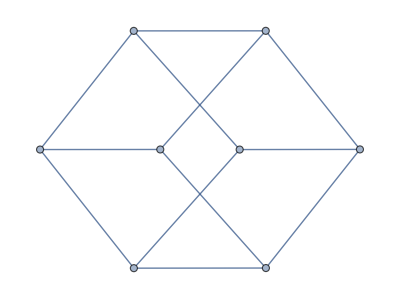
Naming a new polyhedron: p11→-Graphics- Y[10000004,10000005,10000011] Y[10000005,10000007,10000008] Y[10000006,10000004,10000010] Y[10000007,10000006,10000009] Y[10000008,10000012,10000013] Y[10000009,10000014,10000012] Y[10000010,10000015,10000014] Y[10000011,10000013,10000015]

-b^2 d^4 (-2 b+b d+t-d t) (2 b^5 d-b d p11+2 b^4 d t-p11 t-d p11 t-4 b^3 d t^2+2 b d t^4+2 b d^2 t^4)

```mathematica
ip41=Factor[Det[InnerProducts[4,1]]]
```

```mathematica
{Cube}=Complement[Cases[ip41,_Symbol,∞],{d,b,t}];
```

Set::wrsym: Symbol Cube is Protected.

```mathematica
Solve[ip41==0,Cube]
```

{}

```mathematica
AddPolyhedraEvaluations[{1,0,1,1,4}][%]
```

```mathematica
NullSpace[InnerProducts[4,1]/.PolyhedraEvaluationRules[{1,0,1,1,4}]]
```

{}

```mathematica
squareRelation=-Most[%⟦1⟧]
```

Part::partw: Part 1 of {} does not exist.

{}

```mathematica
Together[ApplySquareRelation[squareRelation][Cube/.PolyhedraNames]-(Cube/.PolyhedraEvaluationRules[{1,0,1,1,4}])]
```

-Cube+ApplySquareRelation[{}][Cube]

```mathematica
AddPolyhedraEvaluations[{1,0,1,1,4}][{Cube->(2 b d (b^4+b^3 t-2 b^2 t^2+t^4+d t^4))/(b d+t+d t)}];
```

```mathematica
squareRelation={(b^3+b^2 t-b t^2)/(b d+t+d t),(b^3+b^2 t-b t^2)/(b d+t+d t),(-b^2+t^2+d t^2)/(b d+t+d t),(-b^2+t^2+d t^2)/(b d+t+d t)};
```

```mathematica
AddDiagramReduction[{1,0,1,1,4}][ApplySquareRelation[squareRelation]]
```

```mathematica
VariableSubstitutions[{1,0,1,1,4}]
```

{}

```mathematica
PolyhedraEvaluationRules[{1,0,1,1,4}]
```

{}

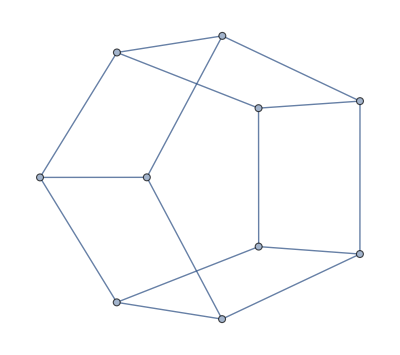
Naming a new polyhedron: p12→-Graphics- Y[10000006,10000014,10000013] Y[10000007,10000006,10000012] Y[10000008,10000007,10000011] Y[10000008,10000010,10000009] Y[10000009,10000015,10000014] Y[10000010,10000016,10000017] Y[10000011,10000018,10000016] Y[10000012,10000019,10000018] Y[10000013,10000020,10000019] Y[10000015,10000017,10000020]

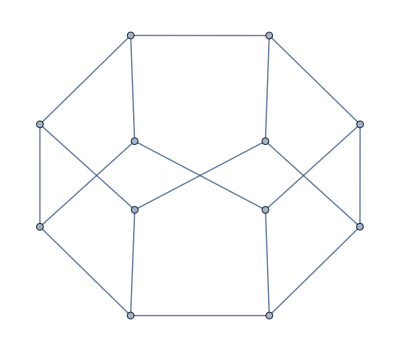
Naming a new polyhedron: p13→-Graphics- Y[10000006,10000008,10000011] Y[10000006,10000017,10000016] Y[10000007,10000008,10000015] Y[10000009,10000007,10000014] Y[10000010,10000009,10000013] Y[10000011,10000010,10000012] Y[10000012,10000019,10000020] Y[10000013,10000021,10000019] Y[10000014,10000022,10000021] Y[10000015,10000016,10000018] Y[10000017,10000020,10000023] Y[10000018,10000023,10000022]

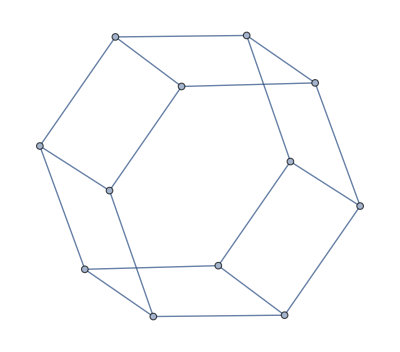
Naming a new polyhedron: p14→-Graphics- Y[10000006,10000007,10000017] Y[10000007,10000011,10000012] Y[10000008,10000006,10000016] Y[10000009,10000008,10000015] Y[10000010,10000009,10000014] Y[10000011,10000010,10000013] Y[10000012,10000018,10000019] Y[10000013,10000020,10000018] Y[10000014,10000021,10000020] Y[10000015,10000022,10000021] Y[10000016,10000023,10000022] Y[10000017,10000019,10000023]

```mathematica
ip61=InnerProductsWithoutSquares[6,1];
```

```mathematica
DisplayPolyhedraNames[]
```

{p11→-Graphics-,p12→-Graphics-,p13→-Graphics-,p14→-Graphics-}

```mathematica
missingPolyhedra=Complement[Cases[ip61,_Symbol|_Prism,∞],{d,b,t}]
```

{p11,p12,p13,p14}

```mathematica
tryToEvaluate[missingPolyhedra:{Symbol___}]:=(AddPolyhedraEvaluations[{1,0,1,1,4}]/@Solve[((Together[ApplySquareRelation[squareRelation][#/.PolyhedraNames]-(#/.PolyhedraEvaluationRules[{1,0,1,1,4}])])/.PolyhedraEvaluationRules[{1,0,1,1,4}])==0,#])&/@missingPolyhedra;
```

```mathematica
tryToEvaluateMissingPolyhedraIn[X_]:=tryToEvaluate[Complement[Cases[X,_Symbol|_Prism,∞],{d,b,t}]]
```

```mathematica
tryToEvaluateMissingPolyhedraIn[ip61]
```

{{Null},{Null},{Null},{Null}}

```mathematica
SavePolyhedraEvaluations[]
```